```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
theoryData=Import[StringJoin["theory-",suffix,".json"], "RawJSON"];
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];

countErr[sample_]:=Block[{total=Total@sample,p},
Function[
p=#/total;Around[#,
3*Sqrt[total/(total-1)*(#*(1-p^2)+(total-#)*p^2)]
]
]/@sample
]
label[sample_Association,labels_]:=Block[{keys=Keys@sample,result},
result=sample;{"Mc","Alg1", "Alg2", "Theory"}
If[!MemberQ[keys,#],result[#]=0]&/@labels;
result
]
```

Suffix: hT

Energy levels: {-10.,-6.,-2.,2.,6.,10.}

Sample sizes: 10000

{{2.940.05,2.650.06,1.10.4,2.940.04,2.950.05},{3.7200.018,3.6930.019,1.860.15,3.7250.012,3.7230.018},{3.5340.023,3.6020.021,3.99590.0022,3.5250.018,3.5270.024},{2.670.06,2.780.05,0.90.5,2.660.06,2.650.06},{1.00.4,1.340.28,-∞,1.10.4,1.150.35},{-∞,-∞,-∞,-1.7.,-∞}}

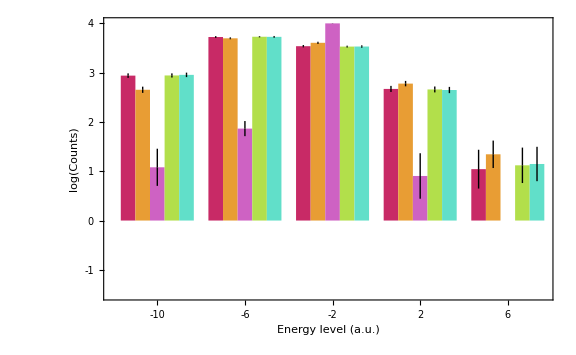

```mathematica
Row@{"Energy levels: ",labels = theoryData["energy_level"]}
{engyMc,engyA1,engyA2} =label[
Counts[#["energy_sample"]],labels
]&/@{mcData,a1Data,a2Data};

Row@{"Sample sizes: ",sampleSize=Total@Values@engyMc}
Assert@And[
sampleSize==Total[Values@engyA1],
sampleSize==Total[Values@engyA2]
]

(* Theory and example of a multinomial sample *)
drb=MultinomialDistribution[sampleSize, theoryData["energy_probs"]];
engyTheory =Association@MapThread[
Rule[#1,#2]&,{labels,sampleSize*theoryData["energy_probs"]}
];
err=3*StandardDeviation@drb;
SeedRandom@0;engyExample=Association@MapThread[
Rule[#1,#2]&,{labels,RandomVariate@drb}
];

(* Adding errors *)
{engyMc,engyA1,engyA2,engyExample}=countErr/@{
engyMc,engyA1,engyA2,engyExample
};
engyTheory=Association@MapThread[
Rule[#1,Around[#2,#3]]&,{Keys@engyTheory,Values@engyTheory,err}
];



Transpose[Log10[
Values[#]
]&/@{KeySort[engyMc],KeySort[engyA1],KeySort[engyA2],engyTheory,engyExample}]

(* Rearranging bars *)
bars=Transpose[Log10[
Most@Values[#]
]&/@{KeySort[engyMc],KeySort[engyA1],KeySort[engyA2],engyTheory,engyExample}];
colors = Table[ColorData[54][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];

BarChart[
bars,ChartStyle->(Directive[EdgeForm@None,FaceForm@#]&/@colors),

PlotRange->{Automatic,{-1.5,4}},

FrameLabel->{
{Log["Counts"],None},{"Energy level (a.u.)",None}
},
FrameTicks->{
{Table[i,{i,-2,5}](*Table[
{i*10^4,Row@{i,"×",Superscript[10,5]}},
{i,1,10,2}
]*),None},
{Join[
Table[{6*i+0.5,Null,{0,0.02}},{i,4}],
Table[{6*i-2.5,Round@labels[[i]],{0,0}},{i,Length@bars}]
],None}
},
FrameTicksStyle->Thickness@0.003,

ChartLayout->"Grouped",BarSpacing->{0,1},
Epilog->{
Inset[Framed[
SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"MC","A1","A2","Theory","Multinomial"},
LegendLayout->"Row",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.4,0.17}]
},

BaseStyle->baseStyle,
Axes->False,Frame->True,FrameStyle->Append[baseStyle,Thickness@0.004],
ImageSize->Large
]
```

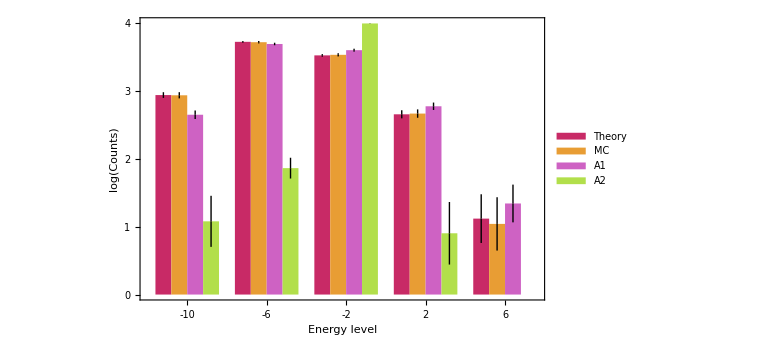

```mathematica
bars=Transpose[Log10[
Most@Values[#]
]&/@{engyTheory,KeySort[engyMc],KeySort[engyA1],KeySort[engyA2]}];
colors = Table[ColorData[54][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->20];
frameStyle = Append[baseStyle, Thickness@0.003];

Legended[
BarChart[
bars,ChartStyle->(Directive[EdgeForm@None,FaceForm@#]&/@colors),

PlotRange->{Automatic,{0,4}},

FrameLabel->{
{Log["Counts"],None},{"Energy level",None}
},
FrameTicks->{
{Table[i,{i,-2,5}](*Table[
{i*10^4,Row@{i,"×",Superscript[10,5]}},
{i,1,10,2}
]*),None},
{Join[
Table[{5*i+0.5,Null,{0,0.02}},{i,4}],
Table[{5*i-2,Round@labels[[i]],{0,0}},{i,Length@bars}]
],None}
},
FrameTicksStyle->Thickness@0.003,

ChartLayout->"Grouped",BarSpacing->{0,1},
(*Epilog->{
Inset[Framed[,FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5],Scaled@{0.4,0.17}]
},*)

BaseStyle->baseStyle,
Axes->False,Frame->True,FrameStyle->Append[baseStyle,Thickness@0.004],
ImageSize->Large, ImageMargins->0
],
Placed[SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"Theory","MC","A1","A2"},
LabelStyle->baseStyle,Alignment->{Center,Center},
LegendMarkerSize->20,LegendLayout->"Row",LegendMargins->0

],Above]
]
```